数据集

特别是在较大的组织中，计算往往以处理大量的结构化数据为中心。Wolfram 语言有一个非常强大的方式来处理结构化数据，使用数据集。

一个简单的例子是，数据集由关联的关联组成。

创建一个简单的数据集，可以看成是有 2 行 3 列：

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

Dataset[<>]

Wolfram 语言将以表格的形式来显示大多数数据集。你可以从数据集中提取部分内容，就像你从关联中提取一样。

从第 b 行第 z 列获取元素：

```mathematica
data["b","z"]
```

7

你可以先提取第 b 行整行，然后获取结果中的“z”元素：

```mathematica
data["b"]["z"]
```

7

你也可以只获取数据集的第 b 行整行。结果是一个新的数据集，为了方便阅读，在这种情况下刚好显示为一个列。

使用原始数据集的第 b 行整行来生成一个新的数据集：

```mathematica
data["b"]
```

Dataset[<>]

这里是对应于所有“行”的“z 列”的数据集。

生成一个由所有行的“z 列”组成的数据集：

```mathematica
data[All,"z"]
```

Dataset[<>]

提取数据集的一部分只是一个开始。在任何你可以查询一部分数据的地方，你也可以给出一个函数，该函数将应用于该层次的所有部分。

通过对所有行的所有列应用 Total，获得每行的总和：

```mathematica
data[All,Total]
```

Dataset[<>]

如果我们用 f 而不是 Total，我们可以看看发生了什么：函数被应用于每个“行”的关联。

对每行应用函数 f：

```mathematica
data[All,f]
```

Dataset[<>]

应用一个函数，将每个关联的 x 和 z 元素相加：

```mathematica
data[All,#x+#z&]
```

Dataset[<>]

你可以使用任何函数；这里是 PieChart：

```mathematica
data[All,PieChart]
```

Dataset[<>]

你也可以给出一个应用于所有行的函数。

这将提取每个“z 列”的值，然后将 f 应用于结果的关联：

```mathematica
data[f,"z"]
```

f[<|a→3,b→7|>]

对所有列的总和应用 f：

```mathematica
data[f,Total]
```

f[<|a→6,b→22|>]

找出这些总和的最大值：

```mathematica
data[Max,Total]
```

22

你总是可以进行“连锁”查询，例如，首先计算所有行的总和，然后取出“b 行”的结果。

计算所有行的总和，然后取出“b 行”的总和：

```mathematica
data[All,Total]["b"]
```

22

它等同于这样：

```mathematica
data["b",Total]
```

22

特别是在处理大型数据集的时候，通常会想根据一个标准来选择部分数据。Select 的运算符形式提供了一个非常方便的方法来做到这一点。

从列表中选择大于 5 的数字：

```mathematica
Select[{1,3,6,8,2,5,9,7},#>5&]
```

{6,8,9,7}

还有一种方法可以得到同样的答案，使用 Select 的运算符形式：

```mathematica
Select[#>5&][{1,3,6,8,2,5,9,7}]
```

{6,8,9,7}

Select 的运算符形式是一个函数，可以应用它来实际执行 Select 操作。

通过只选择“z 列”大于 5 的行来创建一个数据集：

```mathematica
data[Select[#z>5&]]
```

Dataset[<>]

对于每一行，选择数值大于 5 的列，留下一个锯齿状结构：

```mathematica
data[All,Select[#>5&]]
```

Dataset[<>]

Normal 将数据集转换为一个普通的关联的关联：

```mathematica
Normal[%]
```

<|a→<||>,b→<|y→10,z→7|>|>

许多 Wolfram 语言函数都有运算符形式。

根据函数应用于每个元素后的值进行排序：

```mathematica
SortBy[{1,3,6,8,2,5,9,7},If[EvenQ[#],#,10+#]&]
```

{2,6,8,1,3,5,7,9}

SortBy 有一个运算符形式：

```mathematica
SortBy[If[EvenQ[#],#,10+#]&][{1,3,6,8,2,5,9,7}]
```

{2,6,8,1,3,5,7,9}

根据 x 和 y 列的差值对行进行排序：

```mathematica
data[SortBy[#x-#y&]]
```

Dataset[<>]

对各行进行排序，并找出所有列的总和：

```mathematica
data[SortBy[#x-#y&],Total]
```

Dataset[<>]

有时你想对数据集中的每个元素应用函数。

对数据集中的每个元素应用 f：

```mathematica
data[All,All,f]
```

Dataset[<>]

在对其元素的平方进行求和之前，先对各行进行排序：

```mathematica
data[SortBy[#x-#y&],Total,#^2&]
```

Dataset[<>]

数据集可以包含任意的列表和关联的组合。下面是一个数据集，它可以被认为是一个带有命名的字段的记录列表。

使用由关联组成的列表形成的数据集：

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7,"z"->1|>}]
```

Dataset[<>]

某些条目缺失也是可以的：

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7|>}]
```

Dataset[<>]

现在我们已经看过了一些简单的例子，现在是时候看看一些稍微实际的东西了。让我们导入一个给出行星和卫星属性的数据集。这个数据集有一个层级结构，每个行星都有自己的质量和半径，然后还有一个卫星的集合，每个卫星都有自己的属性。这种一般的结构在现实中极为常见(想想学生和成绩，客户和订单，等等)。

从云端获取行星和卫星的层级数据集：

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

Dataset[<>]

找出所有行星的半径：

```mathematica
planets[All,"Radius"]
```

Dataset[<>]

创建行星半径的条形图：

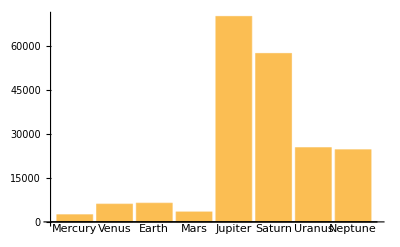

```mathematica
BarChart[planets[All,"Radius"],ChartLabels->Automatic]
```

如果我们询问火星的卫星，我们会得到一个数据集，然后我们可以进一步查询。

获取关于火星卫星的数据集：

```mathematica
planets["Mars","Moons"]
```

Dataset[<>]

进一步挖掘，创建火星所有卫星的半径表：

```mathematica
planets["Mars","Moons",All,"Radius"]
```

Dataset[<>]

我们可以对所有行星的卫星进行计算。首先，让我们找出每个行星有多少个卫星。

为每颗行星的卫星数量创建一个数据集：

```mathematica
planets[All,"Moons",Length]
```

Dataset[<>]

找出每个行星的所有卫星的质量总和：

```mathematica
planets[All,"Moons",Total,"Mass"]
```

Dataset[<>]

得到相同的结果，但只针对有 10 个以上卫星的行星：

```mathematica
planets[Select[Length[#Moons]>10&],"Moons",Total,"Mass"]
```

Dataset[<>]

将结果创建为饼图：

```mathematica
PieChart[%,ChartLegends->Automatic]
```

-Graphics-

获取一个包含超过地球质量 1% 的卫星的数据集。

对于所有的卫星，选择那些质量大于地球质量 0.01 倍的卫星：

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]]
```

Dataset[<>]

获取每个行星的结果关联中的键值(即卫星名称)的列表：

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]][All,Keys]
```

Dataset[<>]

获取底层的关联：

```mathematica
Normal[%]
```

<|Mercury→{},Venus→{},Earth→{Moon},Mars→{},Jupiter→{Callisto,Ganymede,Io},Saturn→{Titan},Uranus→{},Neptune→{}|>

将所有键值列表连接在一起：

```mathematica
Catenate[%]
```

{Moon,Callisto,Ganymede,Io,Titan}

下面是将整个计算放在一行中进行：

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]][Catenate,Keys]//Normal
```

{Moon,Callisto,Ganymede,Io,Titan}

这里还有一个例子，我们找到每个行星质量的对数，然后把每个行星的这些数值做成一个数轴图。

为每个行星的卫星绘制质量对数的数轴图：

```mathematica
planets[All,"Moons",NumberLinePlot[Values[#]]&,Log[#Mass/LinguisticAssistant]&]
```

Dataset[<>]

举最后一个例子，让我们创建一个卫星名称的词云，根据卫星的质量来确定大小。要做到这一点，我们需要一个单一的关联，把每个卫星的名字与它的质量关联起来。

当给定一个关联时，WordCloud 会根据关联中的值来确定大小：

```mathematica
WordCloud[<|"A"->5,"B"->4,"C"->3,"D"->2,"E"->1|>]
```

-Graphics-

函数 Association 用于将关联组合起来：

```mathematica
Association[<|"a"->1,"b"->2|>,<|"c"->3|>]
```

<|a→1,b→2,c→3|>

生成卫星质量的词云：

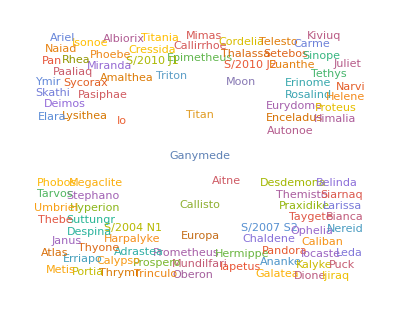

```mathematica
planets[WordCloud[Association[Values[#]]]&,"Moons",All,"Mass"]
```

就其作用而言，这里的代码出奇地简单。但我们可以通过使用 @* 或者 /*来使它稍微精简一些。

我们之前已经看到，我们可以把 f[g[x]] 这样的东西写成 f@g@x 或者 x//g//f。我们也可以把它写成 f[g[#]]&[x]。但是 f[g[#]]& 呢？有没有一种简短的写法呢？答案是有的，使用函数复合运算符 @* 和 /*。

f@*g@*h 表示从右向左应用函数的组合：

```mathematica
(f@*g@*h)[x]
```

f[g[h[x]]]

h/*g/*f 表示从左向右应用函数的组合：

```mathematica
(h/*g/*f)[x]
```

f[g[h[x]]]

下面是使用 @* 来重写的前面的代码：

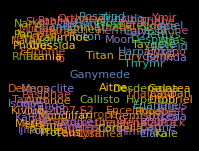

```mathematica
planets[WordCloud@*Association@*Values,"Moons",All,"Mass"]
```

使用右复合 /*：

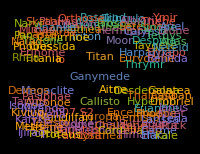

```mathematica
planets[Values/*Association/*WordCloud,"Moons",All,"Mass"]
```

举最后一个例子，让我们看看另一个数据集，这次是直接来自 Wolfram 数据存储库。这里有一个来自存储库的网页(关于大流星)。

-Graphics-

要获得这里提到的主数据集，只需使用 ResourceData。

只需给 ResourceData 提供数据集的名称，就可以获得数据集。

```mathematica
fireballs=ResourceData["Fireballs and Bolides"]
```

Dataset[<>]

提取每一行的坐标项，并绘制结果：

```mathematica
GeoListPlot[fireballs[All,"Coordinates"]]
```

-Graphics-

创建海拔高度的直方图：

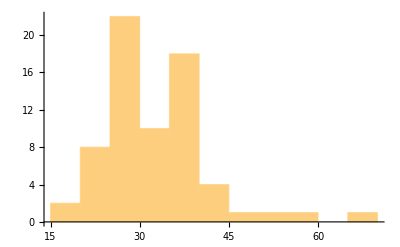

```mathematica
Histogram[fireballs[All,"Altitude"]]
```

词汇

Dataset[data] |   | 一个数据集
Normal[dataset] |   | 将数据集转换为正常的列表和关联
Catenate[{assoc_1, ...}] |   | 连结关联，将它们的元素进行组合
f@*g |   | 复合函数(应用于 x 时就是 f[g[x]])
f/*g |   | 右复合(应用于 x 时就是 g[f[x]])

"共有 13 道习题" | "开始练习 »"

注意：这些练习需要使用数据集 planets=CloudGet["http: // wolfr.am/7FxLgPm5"]。

创建一个行星的词云，其权重由其卫星的数量来决定。»

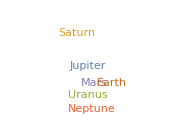
| 期望输出： |  
  | -Graphics- |

将每个行星的卫星数量创建为柱状图。»

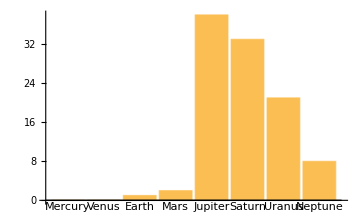
| 期望输出： |  
  | -Graphics- |

创建一个行星质量的数据集，按其卫星的数量进行排序。»

| 期望输出： |  
  | Dataset[<>] |

创建一个行星及其质量最大的卫星的质量的数据集。»

| 期望输出： |  
  | Dataset[<>] |

创建一个行星质量的数据集，按其卫星的最大质量进行排序。»

| 期望输出： |  
  | Dataset[<>] |

创建一个行星及其所有卫星的质量平均值的数据集。»

| 期望输出： |  
  | Dataset[<>] |

对于每颗行星，创建质量大于 0.0001 个地球质量的卫星列表。»

| 期望输出： |  
  | Dataset[<>] |

创建一个中美洲(Central America)国家的词云，国家的名称大小与维基百科上关于它们的文章的长度成正比。»

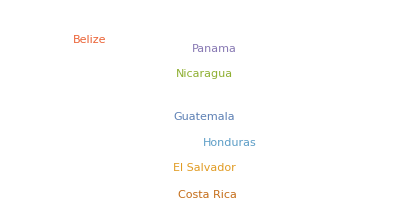
| 期望输出示例： |  
  | -Graphics- |

在 Fireballs & Bolides 数据集中找出最大的观测高度(Altitude)。»

| 期望输出： |  
  | 66.6 "km" |

在 Fireballs & Bolides 数据集中找出 5 个最大观测高度的数据集。»

| 期望输出： |  
  | Dataset[<>] |

在 Fireballs & Bolides 数据集中，对连续的峰值亮度时间的差值创建一个直方图。»

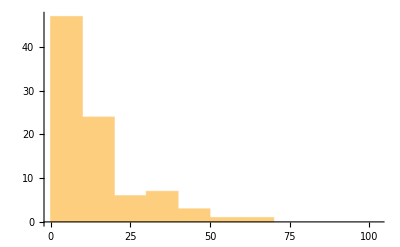
| 期望输出： |  
  | -Graphics- |

绘制出 Fireballs & Bolides 数据集中前 10 个条目的最近城市，并为每个城市添加标签。»

| 期望输出： |  
  | -Graphics- |

绘制出 Fireballs & Bolides 数据集中高度最大的 10 个条目的最近城市，并为每个城市添加标签。»

| 期望输出： |  
  | -Graphics- |

问&答

数据集可以包含哪些类型的数据？

任何类型。不仅仅是数字和文本，还可以是图像、图以及更多其它类型。没有必要让某一行或某一列的所有元素都是同一类型。

我可以将电子表格转换为数据集吗？

可以。SemanticImport 通常是一个很好的方式。

什么是数据库，它们与数据集有什么关系？

数据库是在计算机系统中存储结构化数据的一种传统方式。数据库通常被设置为允许读取和写入数据。数据集是一种表示可能存储在数据库中的数据的方式，用 Wolfram 语言操作起来非常容易。

数据集中的数据与 SQL(关系型)数据库中的数据相比如何？

SQL 数据库严格来说是基于以特定类型的行和列排列的数据表格，并通过“外部键值”来连接其他数据。数据集可以是任何类型的数据组合，可以包含任意数量的嵌套，以及任何层次结构，有点类似于 NoSQL 数据库，但由于语言的符号性质，使得额外的操作成为可能。

我可以使用数据集来为它们建立实体和数值吗？

是的，如果你有一个数据集，它是关联的关联，外部键值为实体，内部键值是属性，那么你只需要把这个放在 EntityStore 里面，就差不多是把一切都设置好了。

技术笔记

数据集支持一种新的符号数据库结构，它概括了关系型数据库和层次型数据库。

数据集中还包括许多我们尚未讨论的其它机制和功能。

对数据集的查询所能做的一切，也可以通过在底层列表和关联上使用 Map 和 Apply 等函数来完成，但通常对数据集的查询会简单得多。

您可以使用 DatabaseLink 来直接将 Wolfram 语言连接到 SQL 数据库，并使用 SQL 语法进行查询。

探索更多

Wolfram 语言中的计算结构化数据集指南 »